```mathematica
SetDirectory["/Users/mobileryan/Triplet-ESR"]
```

/Users/mobileryan/Triplet-ESR

```mathematica
Directory[]
```

/Users/mobileryan

```mathematica
SetDirectory["C:\\Users\\goluc\\Desktop\\nonLinearFit"]
```

C:\Users\goluc\Desktop\nonLinearFit

```mathematica
preData=Import["./test.dat","CSV" ];
{dimT, dump}=Dimensions[preData[[2;;-1]]]
BData=Drop[Drop[preData[[1]],1],-1];
dimB=Length[BData]
DataB[B_]:=Table[{preData[[i,1]],preData[[i,B+1]]},{i,2,dimT}]
DataT[t_]:=Table[{preData[[1,i]],preData[[t+1,i+1]]},{i,1,dimB}]
```

{1002,352}

350

```mathematica
tempData=preData[[2;;-1, 2;;-1]];
ArrayPlot[tempData,ColorFunction->"Rainbow",AspectRatio->1]
{Max[tempData], Min[tempData]}
```

-Graphics-

{Max[41.3406,],Min[-34.1741,]}

```mathematica
Manipulate[
Module[{dataT},
dataT=DataT[startT];
ListPlot[dataT,Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full, PlotLabel->ToString[startT]<>", Time = "<>ToString[preData[[startT+1,1]]]<>", Max = "<> ToString[Max[dataT[[1;;-1,2]]]]<>", Min = "<>ToString[ Min[dataT[[1;;-1,2]]]]] 
],
{{startT,207},1,dimT,1}]
```

```mathematica
Manipulate[
Module[{dataB},
dataB=DataB[startB];
ListPlot[dataB,Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full, PlotLabel->ToString[startB]<>", B-field = "<>ToString[preData[[1,startB]]]<>", Max = "<> ToString[Max[dataB[[1;;-1,2]]]]<>", Min = "<>ToString[ Min[dataB[[1;;-1,2]]]]]
] ,
{{startB,105},1,dimB,1}]
```

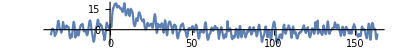

{B-Field,3.209,2.4,mean,0.0624817,sd,3.57825}

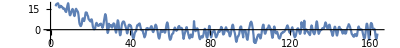

```mathematica
startB=103;
dataB=DataB[startB];
fitStartT=195;
ListPlot[dataB, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full] 
{"B-Field",BData[[startB]],dataB[[fitStartT,1]],"mean",noiseLevel=Mean[dataB[[1;;fitStartT-20,2]]], "sd",sd=StandardDeviation[dataB[[1;;fitStartT-20,2]]]}
g1=ListPlot[dataB[[fitStartT;;-1]], Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
```

```mathematica
Func[t_,a_,Ta_]:=a Exp[-t/Ta]
f[t_,par_]:=Func[t,par[[1]],par[[2]]]+Func[t,par[[3]],par[[4]]]
F[t_,par_]:={ⅇ^(-t/par[[2]]),(par[[1]] ⅇ^(-t/par[[2]]) t)/par[[2]]^2,ⅇ^(-t/par[[4]]),(par[[3]] ⅇ^(-t/par[[4]]) t)/par[[4]]^2}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 1202.47 | 2.48123×10^6 | 0.000484626 | 0.999613
Ta | 33.8702 | 503.189 | 0.0673111 | 0.946351
b | -1180.69 | 2.48123×10^6 | -0.000475848 | 0.99962
Tb | 34.3598 | 516.471 | 0.0665279 | 0.946974, | DF | SS | MS
Model | 4 | 16287.5 | 4071.86
Error | 803 | 7049.26 | 8.77866
Uncorrected Total | 807 | 23336.7 | 
Corrected Total | 806 | 22772.8 | , | Estimate | Standard Error | Confidence Interval
a | 1202.47 | 2.48123×10^6 | {-4.86927×10^6,4.87167×10^6}
Ta | 33.8702 | 503.189 | {-953.85,1021.59}
b | -1180.69 | 2.48123×10^6 | {-4.87165×10^6,4.86929×10^6}
Tb | 34.3598 | 516.471 | {-979.434,1048.15}}

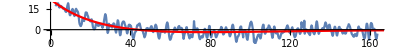

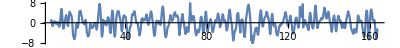

{mean,0.0108697,sd,2.96467,0.828525}

```mathematica
nlm=NonlinearModelFit[dataB[[fitStartT;;-1]],{f[t,{a,Ta,b,Tb}], a>0, b<0, 0<Ta <Tb}, {a, Ta, b, Tb}, t,AccuracyGoal->1, PrecisionGoal->1];
nlm[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
Show[
g1,
Plot[nlm[t],{t,0,200}, PlotRange->All, PlotStyle->Red]
]
diff=Table[{dataB[[i,1]],dataB[[i,2]]-nlm[dataB[[i,1]]]},{i,200,Length[dataB]}];
ListPlot[diff, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
{"mean",Mean[diff[[1;;-1,2]]], "sd",fitSigma=StandardDeviation[diff[[1;;-1,2]]], fitSigma/sd}
```

```mathematica
FindFit[dataB[[fitStartT;;-1]],a Exp[-t/Ta]+b Exp[-t/Tb],{{a,20},{Ta,20},{b,-10},{Tb,80}},t,WorkingPrecision->10]
```

{a→227.8250118,Ta→32.81372156,b→-206.0419142,Tb→35.5086855}

## Manual Method

```mathematica
X=dataB[[fitStartT;;-1]][[1;;-1,1]];
Y=dataB[[fitStartT;;-1]][[1;;-1,2]];
n=Length[X];
SSRcoun= Table[{b, Tb, 
fn =Table[f[X[[i]], {55, 28, b, Tb}],{i,Length[X]}];
SSRn=(Y - fn).(Y-fn)/n},{b,-40,-20, 2}, {Tb, 20, 80,2}];
{mi,mj}=Dimensions[SSRcoun][[{1,2}]];
Min[Table[SSRcoun[[i,j,3]],{i,1,mi},{j,1,mj}]]
%*n
```

8.80606

7106.49

```mathematica
12 n
```

9684

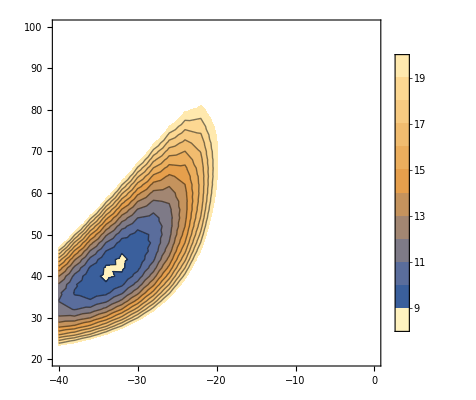

```mathematica
ListContourPlot[Flatten[SSRcoun,1],
PlotRange->{0,20},
Contours->Table[i,{i,7,20,1}],
InterpolationOrder->3,PlotLegends->Automatic]
```

```mathematica
DF=803;α=0.95;
tStat=Table[temp[[1,i]]/temp[[2,i]],{i,1,4}]
pValue=Table[2(1-CDF[StudentTDistribution[DF],Abs[tStat[[i]]]]),{i,1,4}]
CF=Table[
temp[[1,i]]+
temp[[2,i]]{InverseCDF[StudentTDistribution[DF],(1-α)/2],InverseCDF[StudentTDistribution[DF],(1+α)/2]},{i,1,4}]
```

{1.74526,4.84665,-0.678331,2.36191}

{0.0813214,1.50736×10^-6,0.497757,0.018419}

{{-8.03612,136.909},{17.9915,42.4848},{-98.8684,48.0853},{9.37862,101.661}}

```mathematica
newPar2[par_,dataB_]:=Module[
{fa,Fa, Y,X, par1,CoVar, error, var, DF, GMat},
X=dataB[[1;;-1,1]];
Y=dataB[[1;;-1,2]];
fa=Table[Func[X[[i]], par[[1]],par[[2]]],{i,Length[X]}];
Fa=Table[F2[X[[i]], par],{i,Length[X]}];
GMat=Inverse[Transpose[Fa].Fa].Transpose[Fa];
par1=par+GMat.(Y-fa);
DF=Length[X]-Length[par];
var=(Y-fa).(Y-fa)/DF;
CoVar=var Inverse[Transpose[Fa].Fa];
error=Table[√CoVar[[i,i]],{i,1,Length[par]}];
{par1,error, var,DF}
]
```

```mathematica
temp2=newPar2[{50,30},dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
```

{{42.0385,18.115},{1.32321,1.03401},47.0199,805}

{{43.21,18.0827},{0.909289,0.483381},10.8097,805}

{{43.1979,18.0916},{0.908267,0.468798},10.7557,805}

{{43.2012,18.0894},{0.907925,0.469012},10.7557,805}

{{43.2004,18.0899},{0.908009,0.468955},10.7557,805}

{{43.2006,18.0898},{0.907988,0.468969},10.7557,805}

{{43.2005,18.0898},{0.907994,0.468966},10.7557,805}

{{43.2005,18.0898},{0.907992,0.468966},10.7557,805}

```mathematica
nlm2[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 43.2005 | 0.907993 | 47.5781 | 3.98102×10^-236
Ta | 18.0898 | 0.468966 | 38.5738 | 3.69199×10^-185, | DF | SS | MS
Model | 2 | 64018.5 | 32009.3
Error | 805 | 8658.36 | 10.7557
Uncorrected Total | 807 | 72676.9 | 
Corrected Total | 806 | 64550.3 | , | Estimate | Standard Error | Confidence Interval
a | 43.2005 | 0.907993 | {41.4182,44.9828}
Ta | 18.0898 | 0.468966 | {17.1693,19.0104}}

```mathematica
DF2=805;α=0.95;
tStat2=Table[temp2[[1,i]]/temp2[[2,i]],{i,1,2}]
pValue2=Table[2(1-CDF[StudentTDistribution[DF2],Abs[tStat2[[i]]]]),{i,1,2}]
CF2=Table[
temp2[[1,i]]+
temp2[[2,i]]{InverseCDF[StudentTDistribution[DF2],(1-α)/2],InverseCDF[StudentTDistribution[DF2],(1+α)/2]},{i,1,2}]
```

{47.5777,38.5742}

{0.,0.}

{{41.4182,44.9828},{17.1693,19.0104}}